# Call Python to compute CY metrics

Getting started
The easiest thing to get started would be to just run the entire notebook.

Documentation
• To see all functions currently available run ?cymetric
• If you want to see detailed documentation for any of the functions (including its input, options, output, examples), run e.g. ?TrainNN. Running Options[TrainNN] gives you a list of the options for this function and their default values. 
• The value of all global options can be checked with GetGlobalOptions[]

Setting up the program
In order to install the program, you just need to call Setup[] (Setup will detect whether you have run it before and not do anything if everything is already setup; so it does not hurt to just compile the entire notebook every time). Setup[] will try to discover python3 on your system and create a virtual environment with all required packages installed. For some combinations of Python and (older versions of) Mathematica, setup will automatically apply a bug fix. The program will create a text file (with the same name as the notebook, with an extension “.m”, at the same location as the notebook file) that stores some options, e.g. the location of the virtual environment to use for future runs.
More advanced (if you do not want to just call Setup[] and be done with it):
1.) If you already have a python environment that you want to use, you need to “pip install --user pyzmq” for it to work with Mathematica.  
2.) Then setup the package to use this python interpreter with ChangeSetting[“Python”,”<path/to/python>”].

## Setup Python for CY metrics

Load the package from the web.
You can also download the package file and copy it to Mathematica’s Application folder. 
To find the folder execute the following command in Mathematica: FileNameJoin[{$UserBaseDirectory,”/Applications”}] 
Then just copy the file https://github.com/pythoncymetric/cymetric/tree/main/cymetric/wolfram/cymetric.m to this directory and load it with  <<cymetric`

```mathematica
Get["https://raw.githubusercontent.com/pythoncymetric/cymetric/main/cymetric/wolfram/cymetric.m"];
```

```mathematica
(*Path where the virtual environment for python will be created. Defaults to the User's Home Directory*)
PathToVenv=FileNameJoin[{$HomeDirectory,"venv-mathematica"}];
(*If you already have an environment that you want to use, set the path here*)
(*ChangeSetting["Python","<path/to/python>"]*)
python=Setup[PathToVenv];
```

Mathematica discovered the following Python environments on your system:

Looking for Python 3

Found Python version 3.9.10 at /Library/Frameworks/Python.framework/Versions/Current/bin/python3.9.

Creating virtual environment at /Users/ruehle/venv-mathematica

Upgrading pip, wheel, setuptools...

Installing h5py...

Installing joblib...

Installing numpy...

Installing pyyaml...

Installing pyzmq...

Installing scipy...

Installing sympy...

Installing wolframclient...

Installing cymetric...

Registering venv with mathematica...

Checking whether 'externalevaluate.py' needs to be patched for this version...

Testing new environment...

Everything is working!

## Quintic

### Compute Points and Metric

To look at the parameters and options of a function, simply call ?<FunctionName> and Options[<FunctionName>]

```mathematica
?GeneratePoints
Options[GeneratePoints]
```

{KahlerModuli→{},Points→200000}

Now we generate some points. We set the output Directory to “Quintic”

```mathematica
outDir=FileNameJoin[{NotebookDirectory[],"Quintic"}];
ChangeSetting["Dir",outDir];
```

```mathematica
poly={Subscript[z, 0]^5+Subscript[z, 1]^5+Subscript[z, 2]^5+Subscript[z, 3]^5+Subscript[z, 4]^5+10 Subscript[z, 0] Subscript[z, 1] Subscript[z, 2] Subscript[z, 3] Subscript[z, 4]};
res=GeneratePoints[poly,{4},"Points"->100000,"KahlerModuli"->{1}];
```

Warning: No variables specified, assuming alphabetical monomial ordering.

Generating 100000 points...

Configuration matrix: {{5}}

Number of Parameters per P^n: {1}

Number of points on CY from one ambient space intersection: 5

Now generating 100000 points...

done.

Writing points to /Users/ruehle/GitHub/cymetric/notebooks/Quintic/points.pickle

Now we train the NN. We choose the PhiFS model here. (Training can be made faster if one sets “EvaluateModel”->False). 
We also set Verbose to 3 to see some more info during the training process.

```mathematica
GetSession[]
```

ExternalSessionObject[…]

```mathematica
history=TrainNN["Epochs"->50,"EvaluateModel"->True,"Verbose"->3];
```

DEBUG:mathematica:{'ActivationFunctions': array(['gelu', 'gelu', 'gelu'], dtype='<U4'), 'Alphas': array([1., 1., 1., 1., 1.]), 'BatchSizes': array([   64, 50000]), 'Dir': '/Users/ruehle/GitHub/cymetric/notebooks/Quintic', 'DisableGPU': False, 'HiddenLayers': array([64, 64, 64]), 'LearningRate': 0.001, 'Model': 'PhiFS', 'Precision': 10, 'PrintLosses': array([ True,  True,  True,  True,  True]), 'PrintMeasures': array([ True,  True,  True,  True,  True]), 'Python': '/Users/ruehle/venv-mathematica/bin/python', 'Verbose': 3, 'Epochs': 50, 'EvaluateModel': True, 'logger_level': 10}

DEBUG:mathematica:Using CPU for computation.

DEBUG:mathematica:Model: "sequential"

DEBUG:mathematica:_________________________________________________________________

DEBUG:mathematica: Layer (type)                Output Shape              Param #

DEBUG:mathematica:=================================================================

DEBUG:mathematica: dense (Dense)               (None, 64)                704

DEBUG:mathematica:

DEBUG:mathematica: dense_1 (Dense)             (None, 64)                4160

DEBUG:mathematica:

DEBUG:mathematica: dense_2 (Dense)             (None, 64)                4160

DEBUG:mathematica:

DEBUG:mathematica: dense_3 (Dense)             (None, 1)                 64

DEBUG:mathematica:

DEBUG:mathematica:=================================================================

DEBUG:mathematica:Total params: 9,088

DEBUG:mathematica:Trainable params: 9,088

DEBUG:mathematica:Non-trainable params: 0

DEBUG:mathematica:_________________________________________________________________

Epoch  1/50

- Sigma measure val:      0.2512

- Kaehler measure val:    5.4166e-15

- Transition measure val: 0.0092

- Ricci measure val:      0.8215

- Sigma measure val:      0.1332

- Kaehler measure val:    5.5629e-15

- Transition measure val: 0.0031

- Ricci measure val:      1.1133

1407/1407 - 19s - sigma_loss: 0.1615 - kaehler_loss: 0.0000e+00 - transition_loss: 0.0056 - ricci_loss: 0.0000e+00 - sigma_val: 0.1332 - kaehler_val: 5.5629e-15 - transition_val: 0.0031 - ricci_val: 1.1133 - 19s/epoch - 13ms/step

- Volk val:               4.7830

- Volk val:               5.2553

2/2 - 8s - sigma_loss: 0.0000e+00 - kaehler_loss: 0.0000e+00 - transition_loss: 0.0000e+00 - ricci_loss: 0.0000e+00 - volk_val: 5.2553 - 8s/epoch - 4s/step

Epoch  2/50

- Sigma measure val:      0.1329

- Kaehler measure val:    5.7606e-15

- Transition measure val: 0.0031

- Ricci measure val:      1.2467

- Sigma measure val:      0.1113

- Kaehler measure val:    5.8731e-15

- Transition measure val: 0.0022

- Ricci measure val:      0.6128

1407/1407 - 17s - sigma_loss: 0.1276 - kaehler_loss: 0.0000e+00 - transition_loss: 0.0024 - ricci_loss: 0.0000e+00 - sigma_val: 0.1113 - kaehler_val: 5.8731e-15 - transition_val: 0.0022 - ricci_val: 0.6128 - 17s/epoch - 12ms/step

- Volk val:               4.7982

- Volk val:               5.1006

2/2 - 8s - sigma_loss: 0.0000e+00 - kaehler_loss: 0.0000e+00 - transition_loss: 0.0000e+00 - ricci_loss: 0.0000e+00 - volk_val: 5.1006 - 8s/epoch - 4s/step

Epoch  3/50

- Sigma measure val:      0.1129

- Kaehler measure val:    5.9623e-15

- Transition measure val: 0.0026

- Ricci measure val:      0.6741

- Sigma measure val:      0.0977

- Kaehler measure val:    6.3934e-15

- Transition measure val: 0.0025

- Ricci measure val:      0.6356

1407/1407 - 16s - sigma_loss: 0.1004 - kaehler_loss: 0.0000e+00 - transition_loss: 0.0025 - ricci_loss: 0.0000e+00 - sigma_val: 0.0977 - kaehler_val: 6.3934e-15 - transition_val: 0.0025 - ricci_val: 0.6356 - 16s/epoch - 11ms/step

- Volk val:               4.9990

- Volk val:               4.9108

2/2 - 6s - sigma_loss: 0.0000e+00 - kaehler_loss: 0.0000e+00 - transition_loss: 0.0000e+00 - ricci_loss: 0.0000e+00 - volk_val: 4.9108 - 6s/epoch - 3s/step

Epoch  4/50

- Sigma measure val:      0.1016

- Kaehler measure val:    6.4096e-15

- Transition measure val: 0.0025

- Ricci measure val:      0.6390

- Sigma measure val:      0.0872

- Kaehler measure val:    6.3435e-15

- Transition measure val: 0.0018

- Ricci measure val:      0.5697

1407/1407 - 18s - sigma_loss: 0.0845 - kaehler_loss: 0.0000e+00 - transition_loss: 0.0022 - ricci_loss: 0.0000e+00 - sigma_val: 0.0872 - kaehler_val: 6.3435e-15 - transition_val: 0.0018 - ricci_val: 0.5697 - 18s/epoch - 12ms/step

- Volk val:               4.8932

- Volk val:               5.0105

2/2 - 7s - sigma_loss: 0.0000e+00 - kaehler_loss: 0.0000e+00 - transition_loss: 0.0000e+00 - ricci_loss: 0.0000e+00 - volk_val: 5.0105 - 7s/epoch - 3s/step

Epoch  5/50

- Sigma measure val:      0.0884

- Kaehler measure val:    6.4897e-15

- Transition measure val: 0.0019

- Ricci measure val:      0.5838

- Sigma measure val:      0.0821

- Kaehler measure val:    6.2975e-15

- Transition measure val: 0.0015

- Ricci measure val:      0.5815

1407/1407 - 17s - sigma_loss: 0.0786 - kaehler_loss: 0.0000e+00 - transition_loss: 0.0018 - ricci_loss: 0.0000e+00 - sigma_val: 0.0821 - kaehler_val: 6.2975e-15 - transition_val: 0.0015 - ricci_val: 0.5815 - 17s/epoch - 12ms/step

- Volk val:               4.9463

- Volk val:               5.0645

2/2 - 7s - sigma_loss: 0.0000e+00 - kaehler_loss: 0.0000e+00 - transition_loss: 0.0000e+00 - ricci_loss: 0.0000e+00 - volk_val: 5.0645 - 7s/epoch - 3s/step

Epoch  6/50

- Sigma measure val:      0.0816

- Kaehler measure val:    6.2993e-15

- Transition measure val: 0.0016

- Ricci measure val:      0.5872

- Sigma measure val:      0.0801

- Kaehler measure val:    6.0440e-15

- Transition measure val: 0.0015

- Ricci measure val:      0.5789

1407/1407 - 19s - sigma_loss: 0.0754 - kaehler_loss: 0.0000e+00 - transition_loss: 0.0015 - ricci_loss: 0.0000e+00 - sigma_val: 0.0801 - kaehler_val: 6.0440e-15 - transition_val: 0.0015 - ricci_val: 0.5789 - 19s/epoch - 13ms/step

- Volk val:               4.6884

- Volk val:               4.7585

2/2 - 8s - sigma_loss: 0.0000e+00 - kaehler_loss: 0.0000e+00 - transition_loss: 0.0000e+00 - ricci_loss: 0.0000e+00 - volk_val: 4.7585 - 8s/epoch - 4s/step

Epoch  7/50

- Sigma measure val:      0.0823

- Kaehler measure val:    6.0766e-15

- Transition measure val: 0.0013

- Ricci measure val:      0.5916

- Sigma measure val:      0.0762

- Kaehler measure val:    6.1626e-15

- Transition measure val: 0.0011

- Ricci measure val:      0.5500

1407/1407 - 18s - sigma_loss: 0.0720 - kaehler_loss: 0.0000e+00 - transition_loss: 0.0012 - ricci_loss: 0.0000e+00 - sigma_val: 0.0762 - kaehler_val: 6.1626e-15 - transition_val: 0.0011 - ricci_val: 0.5500 - 18s/epoch - 13ms/step

- Volk val:               4.9791

- Volk val:               5.0849

2/2 - 7s - sigma_loss: 0.0000e+00 - kaehler_loss: 0.0000e+00 - transition_loss: 0.0000e+00 - ricci_loss: 0.0000e+00 - volk_val: 5.0849 - 7s/epoch - 3s/step

Epoch  8/50

- Sigma measure val:      0.0768

- Kaehler measure val:    6.1763e-15

- Transition measure val: 0.0012

- Ricci measure val:      0.5535

- Sigma measure val:      0.0771

- Kaehler measure val:    6.0970e-15

- Transition measure val: 9.4518e-04

- Ricci measure val:      0.5497

1407/1407 - 18s - sigma_loss: 0.0702 - kaehler_loss: 0.0000e+00 - transition_loss: 0.0010 - ricci_loss: 0.0000e+00 - sigma_val: 0.0771 - kaehler_val: 6.0970e-15 - transition_val: 9.4518e-04 - ricci_val: 0.5497 - 18s/epoch - 13ms/step

- Volk val:               4.8217

- Volk val:               4.8642

2/2 - 7s - sigma_loss: 0.0000e+00 - kaehler_loss: 0.0000e+00 - transition_loss: 0.0000e+00 - ricci_loss: 0.0000e+00 - volk_val: 4.8642 - 7s/epoch - 4s/step

Epoch  9/50

- Sigma measure val:      0.0791

- Kaehler measure val:    6.2279e-15

- Transition measure val: 0.0010

- Ricci measure val:      0.5691

- Sigma measure val:      0.0761

- Kaehler measure val:    5.9777e-15

- Transition measure val: 8.2825e-04

- Ricci measure val:      0.5164

1407/1407 - 16s - sigma_loss: 0.0694 - kaehler_loss: 0.0000e+00 - transition_loss: 9.2498e-04 - ricci_loss: 0.0000e+00 - sigma_val: 0.0761 - kaehler_val: 5.9777e-15 - transition_val: 8.2825e-04 - ricci_val: 0.5164 - 16s/epoch - 11ms/step

- Volk val:               4.9194

- Volk val:               4.9950

2/2 - 6s - sigma_loss: 0.0000e+00 - kaehler_loss: 0.0000e+00 - transition_loss: 0.0000e+00 - ricci_loss: 0.0000e+00 - volk_val: 4.9950 - 6s/epoch - 3s/step

Epoch 10/50

- Sigma measure val:      0.0772

- Kaehler measure val:    6.1489e-15

- Transition measure val: 9.1847e-04

- Ricci measure val:      0.5241

- Sigma measure val:      0.0751

- Kaehler measure val:    6.0426e-15

- Transition measure val: 7.4343e-04

- Ricci measure val:      0.5060

1407/1407 - 16s - sigma_loss: 0.0684 - kaehler_loss: 0.0000e+00 - transition_loss: 8.0812e-04 - ricci_loss: 0.0000e+00 - sigma_val: 0.0751 - kaehler_val: 6.0426e-15 - transition_val: 7.4343e-04 - ricci_val: 0.5060 - 16s/epoch - 11ms/step

- Volk val:               4.8911

- Volk val:               4.9860

2/2 - 9s - sigma_loss: 0.0000e+00 - kaehler_loss: 0.0000e+00 - transition_loss: 0.0000e+00 - ricci_loss: 0.0000e+00 - volk_val: 4.9860 - 9s/epoch - 5s/step

Epoch 11/50

- Sigma measure val:      0.0753

- Kaehler measure val:    6.1421e-15

- Transition measure val: 9.9975e-04

- Ricci measure val:      0.5148

- Sigma measure val:      0.0748

- Kaehler measure val:    6.0046e-15

- Transition measure val: 6.4001e-04

- Ricci measure val:      0.5098

1407/1407 - 16s - sigma_loss: 0.0677 - kaehler_loss: 0.0000e+00 - transition_loss: 7.2943e-04 - ricci_loss: 0.0000e+00 - sigma_val: 0.0748 - kaehler_val: 6.0046e-15 - transition_val: 6.4001e-04 - ricci_val: 0.5098 - 16s/epoch - 12ms/step

- Volk val:               4.8549

- Volk val:               4.9119

2/2 - 7s - sigma_loss: 0.0000e+00 - kaehler_loss: 0.0000e+00 - transition_loss: 0.0000e+00 - ricci_loss: 0.0000e+00 - volk_val: 4.9119 - 7s/epoch - 4s/step

Epoch 12/50

- Sigma measure val:      0.0755

- Kaehler measure val:    6.0863e-15

- Transition measure val: 6.0627e-04

- Ricci measure val:      0.5202

- Sigma measure val:      0.0744

- Kaehler measure val:    6.0144e-15

- Transition measure val: 6.2599e-04

- Ricci measure val:      0.5241

1407/1407 - 16s - sigma_loss: 0.0673 - kaehler_loss: 0.0000e+00 - transition_loss: 6.6997e-04 - ricci_loss: 0.0000e+00 - sigma_val: 0.0744 - kaehler_val: 6.0144e-15 - transition_val: 6.2599e-04 - ricci_val: 0.5241 - 16s/epoch - 11ms/step

- Volk val:               4.9042

- Volk val:               4.9456

2/2 - 7s - sigma_loss: 0.0000e+00 - kaehler_loss: 0.0000e+00 - transition_loss: 0.0000e+00 - ricci_loss: 0.0000e+00 - volk_val: 4.9456 - 7s/epoch - 3s/step

Epoch 13/50

- Sigma measure val:      0.0745

- Kaehler measure val:    6.0612e-15

- Transition measure val: 6.9678e-04

- Ricci measure val:      0.5312

- Sigma measure val:      0.0740

- Kaehler measure val:    6.0711e-15

- Transition measure val: 5.9414e-04

- Ricci measure val:      0.4982

1407/1407 - 16s - sigma_loss: 0.0666 - kaehler_loss: 0.0000e+00 - transition_loss: 6.3205e-04 - ricci_loss: 0.0000e+00 - sigma_val: 0.0740 - kaehler_val: 6.0711e-15 - transition_val: 5.9414e-04 - ricci_val: 0.4982 - 16s/epoch - 11ms/step

- Volk val:               4.8483

- Volk val:               4.8700

2/2 - 6s - sigma_loss: 0.0000e+00 - kaehler_loss: 0.0000e+00 - transition_loss: 0.0000e+00 - ricci_loss: 0.0000e+00 - volk_val: 4.8700 - 6s/epoch - 3s/step

Epoch 14/50

- Sigma measure val:      0.0751

- Kaehler measure val:    5.9930e-15

- Transition measure val: 6.3620e-04

- Ricci measure val:      0.5126

- Sigma measure val:      0.0755

- Kaehler measure val:    6.0442e-15

- Transition measure val: 5.0997e-04

- Ricci measure val:      0.4897

1407/1407 - 16s - sigma_loss: 0.0662 - kaehler_loss: 0.0000e+00 - transition_loss: 5.7992e-04 - ricci_loss: 0.0000e+00 - sigma_val: 0.0755 - kaehler_val: 6.0442e-15 - transition_val: 5.0997e-04 - ricci_val: 0.4897 - 16s/epoch - 12ms/step

- Volk val:               4.8907

- Volk val:               4.9476

2/2 - 7s - sigma_loss: 0.0000e+00 - kaehler_loss: 0.0000e+00 - transition_loss: 0.0000e+00 - ricci_loss: 0.0000e+00 - volk_val: 4.9476 - 7s/epoch - 3s/step

Epoch 15/50

- Sigma measure val:      0.0770

- Kaehler measure val:    6.0421e-15

- Transition measure val: 5.1073e-04

- Ricci measure val:      0.4914

- Sigma measure val:      0.0746

- Kaehler measure val:    5.8988e-15

- Transition measure val: 4.7550e-04

- Ricci measure val:      0.4853

1407/1407 - 16s - sigma_loss: 0.0657 - kaehler_loss: 0.0000e+00 - transition_loss: 5.3970e-04 - ricci_loss: 0.0000e+00 - sigma_val: 0.0746 - kaehler_val: 5.8988e-15 - transition_val: 4.7550e-04 - ricci_val: 0.4853 - 16s/epoch - 12ms/step

- Volk val:               4.8758

- Volk val:               4.9063

2/2 - 7s - sigma_loss: 0.0000e+00 - kaehler_loss: 0.0000e+00 - transition_loss: 0.0000e+00 - ricci_loss: 0.0000e+00 - volk_val: 4.9063 - 7s/epoch - 3s/step

Epoch 16/50

- Sigma measure val:      0.0755

- Kaehler measure val:    6.0035e-15

- Transition measure val: 4.9700e-04

- Ricci measure val:      0.4901

- Sigma measure val:      0.0738

- Kaehler measure val:    5.8794e-15

- Transition measure val: 4.9964e-04

- Ricci measure val:      0.4859

1407/1407 - 17s - sigma_loss: 0.0653 - kaehler_loss: 0.0000e+00 - transition_loss: 5.2344e-04 - ricci_loss: 0.0000e+00 - sigma_val: 0.0738 - kaehler_val: 5.8794e-15 - transition_val: 4.9964e-04 - ricci_val: 0.4859 - 17s/epoch - 12ms/step

- Volk val:               4.8077

- Volk val:               4.8361

2/2 - 10s - sigma_loss: 0.0000e+00 - kaehler_loss: 0.0000e+00 - transition_loss: 0.0000e+00 - ricci_loss: 0.0000e+00 - volk_val: 4.8361 - 10s/epoch - 5s/step

Epoch 17/50

- Sigma measure val:      0.0744

- Kaehler measure val:    5.9142e-15

- Transition measure val: 5.0059e-04

- Ricci measure val:      0.4846

- Sigma measure val:      0.0729

- Kaehler measure val:    6.0595e-15

- Transition measure val: 5.2381e-04

- Ricci measure val:      0.5083

1407/1407 - 16s - sigma_loss: 0.0650 - kaehler_loss: 0.0000e+00 - transition_loss: 5.0818e-04 - ricci_loss: 0.0000e+00 - sigma_val: 0.0729 - kaehler_val: 6.0595e-15 - transition_val: 5.2381e-04 - ricci_val: 0.5083 - 16s/epoch - 12ms/step

- Volk val:               4.9082

- Volk val:               4.9542

2/2 - 7s - sigma_loss: 0.0000e+00 - kaehler_loss: 0.0000e+00 - transition_loss: 0.0000e+00 - ricci_loss: 0.0000e+00 - volk_val: 4.9542 - 7s/epoch - 4s/step

Epoch 18/50

- Sigma measure val:      0.0737

- Kaehler measure val:    6.1271e-15

- Transition measure val: 5.8614e-04

- Ricci measure val:      0.5209

- Sigma measure val:      0.0725

- Kaehler measure val:    5.9655e-15

- Transition measure val: 5.1659e-04

- Ricci measure val:      0.4958

1407/1407 - 17s - sigma_loss: 0.0643 - kaehler_loss: 0.0000e+00 - transition_loss: 4.9588e-04 - ricci_loss: 0.0000e+00 - sigma_val: 0.0725 - kaehler_val: 5.9655e-15 - transition_val: 5.1659e-04 - ricci_val: 0.4958 - 17s/epoch - 12ms/step

- Volk val:               4.8194

- Volk val:               4.8137

2/2 - 7s - sigma_loss: 0.0000e+00 - kaehler_loss: 0.0000e+00 - transition_loss: 0.0000e+00 - ricci_loss: 0.0000e+00 - volk_val: 4.8137 - 7s/epoch - 3s/step

Epoch 19/50

- Sigma measure val:      0.0728

- Kaehler measure val:    5.9846e-15

- Transition measure val: 5.1476e-04

- Ricci measure val:      0.4990

- Sigma measure val:      0.0710

- Kaehler measure val:    5.9589e-15

- Transition measure val: 5.3548e-04

- Ricci measure val:      0.4796

1407/1407 - 17s - sigma_loss: 0.0634 - kaehler_loss: 0.0000e+00 - transition_loss: 5.0800e-04 - ricci_loss: 0.0000e+00 - sigma_val: 0.0710 - kaehler_val: 5.9589e-15 - transition_val: 5.3548e-04 - ricci_val: 0.4796 - 17s/epoch - 12ms/step

- Volk val:               4.8360

- Volk val:               4.8738

2/2 - 6s - sigma_loss: 0.0000e+00 - kaehler_loss: 0.0000e+00 - transition_loss: 0.0000e+00 - ricci_loss: 0.0000e+00 - volk_val: 4.8738 - 6s/epoch - 3s/step

Epoch 20/50

- Sigma measure val:      0.0714

- Kaehler measure val:    6.0105e-15

- Transition measure val: 4.9975e-04

- Ricci measure val:      0.4859

- Sigma measure val:      0.0719

- Kaehler measure val:    5.9836e-15

- Transition measure val: 6.4421e-04

- Ricci measure val:      0.4762

1407/1407 - 17s - sigma_loss: 0.0625 - kaehler_loss: 0.0000e+00 - transition_loss: 5.0892e-04 - ricci_loss: 0.0000e+00 - sigma_val: 0.0719 - kaehler_val: 5.9836e-15 - transition_val: 6.4421e-04 - ricci_val: 0.4762 - 17s/epoch - 12ms/step

- Volk val:               4.8512

- Volk val:               4.8580

2/2 - 11s - sigma_loss: 0.0000e+00 - kaehler_loss: 0.0000e+00 - transition_loss: 0.0000e+00 - ricci_loss: 0.0000e+00 - volk_val: 4.8580 - 11s/epoch - 5s/step

Epoch 21/50

- Sigma measure val:      0.0730

- Kaehler measure val:    5.9194e-15

- Transition measure val: 6.5070e-04

- Ricci measure val:      0.4752

- Sigma measure val:      0.0690

- Kaehler measure val:    5.9861e-15

- Transition measure val: 5.2252e-04

- Ricci measure val:      0.4721

1407/1407 - 17s - sigma_loss: 0.0612 - kaehler_loss: 0.0000e+00 - transition_loss: 5.3051e-04 - ricci_loss: 0.0000e+00 - sigma_val: 0.0690 - kaehler_val: 5.9861e-15 - transition_val: 5.2252e-04 - ricci_val: 0.4721 - 17s/epoch - 12ms/step

- Volk val:               4.8814

- Volk val:               4.9213

2/2 - 7s - sigma_loss: 0.0000e+00 - kaehler_loss: 0.0000e+00 - transition_loss: 0.0000e+00 - ricci_loss: 0.0000e+00 - volk_val: 4.9213 - 7s/epoch - 4s/step

Epoch 22/50

- Sigma measure val:      0.0693

- Kaehler measure val:    6.0180e-15

- Transition measure val: 5.1931e-04

- Ricci measure val:      0.4761

- Sigma measure val:      0.0681

- Kaehler measure val:    5.9875e-15

- Transition measure val: 5.6969e-04

- Ricci measure val:      0.4698

1407/1407 - 17s - sigma_loss: 0.0601 - kaehler_loss: 0.0000e+00 - transition_loss: 5.4712e-04 - ricci_loss: 0.0000e+00 - sigma_val: 0.0681 - kaehler_val: 5.9875e-15 - transition_val: 5.6969e-04 - ricci_val: 0.4698 - 17s/epoch - 12ms/step

- Volk val:               4.9198

- Volk val:               4.9636

2/2 - 7s - sigma_loss: 0.0000e+00 - kaehler_loss: 0.0000e+00 - transition_loss: 0.0000e+00 - ricci_loss: 0.0000e+00 - volk_val: 4.9636 - 7s/epoch - 3s/step

Epoch 23/50

- Sigma measure val:      0.0697

- Kaehler measure val:    6.0259e-15

- Transition measure val: 5.8147e-04

- Ricci measure val:      0.4700

- Sigma measure val:      0.0668

- Kaehler measure val:    6.0661e-15

- Transition measure val: 5.6027e-04

- Ricci measure val:      0.4636

1407/1407 - 17s - sigma_loss: 0.0587 - kaehler_loss: 0.0000e+00 - transition_loss: 5.3808e-04 - ricci_loss: 0.0000e+00 - sigma_val: 0.0668 - kaehler_val: 6.0661e-15 - transition_val: 5.6027e-04 - ricci_val: 0.4636 - 17s/epoch - 12ms/step

- Volk val:               4.9056

- Volk val:               4.9377

2/2 - 6s - sigma_loss: 0.0000e+00 - kaehler_loss: 0.0000e+00 - transition_loss: 0.0000e+00 - ricci_loss: 0.0000e+00 - volk_val: 4.9377 - 6s/epoch - 3s/step

Epoch 24/50

- Sigma measure val:      0.0681

- Kaehler measure val:    5.9412e-15

- Transition measure val: 5.5437e-04

- Ricci measure val:      0.4644

- Sigma measure val:      0.0642

- Kaehler measure val:    6.0085e-15

- Transition measure val: 5.3673e-04

- Ricci measure val:      0.4610

1407/1407 - 17s - sigma_loss: 0.0575 - kaehler_loss: 0.0000e+00 - transition_loss: 5.6171e-04 - ricci_loss: 0.0000e+00 - sigma_val: 0.0642 - kaehler_val: 6.0085e-15 - transition_val: 5.3673e-04 - ricci_val: 0.4610 - 17s/epoch - 12ms/step

- Volk val:               4.8985

- Volk val:               4.9353

2/2 - 7s - sigma_loss: 0.0000e+00 - kaehler_loss: 0.0000e+00 - transition_loss: 0.0000e+00 - ricci_loss: 0.0000e+00 - volk_val: 4.9353 - 7s/epoch - 3s/step

Epoch 25/50

- Sigma measure val:      0.0644

- Kaehler measure val:    6.0619e-15

- Transition measure val: 5.4027e-04

- Ricci measure val:      0.4642

- Sigma measure val:      0.0626

- Kaehler measure val:    6.1357e-15

- Transition measure val: 5.5413e-04

- Ricci measure val:      0.4505

1407/1407 - 17s - sigma_loss: 0.0562 - kaehler_loss: 0.0000e+00 - transition_loss: 5.6858e-04 - ricci_loss: 0.0000e+00 - sigma_val: 0.0626 - kaehler_val: 6.1357e-15 - transition_val: 5.5413e-04 - ricci_val: 0.4505 - 17s/epoch - 12ms/step

- Volk val:               4.9520

- Volk val:               4.9757

2/2 - 12s - sigma_loss: 0.0000e+00 - kaehler_loss: 0.0000e+00 - transition_loss: 0.0000e+00 - ricci_loss: 0.0000e+00 - volk_val: 4.9757 - 12s/epoch - 6s/step

Epoch 26/50

- Sigma measure val:      0.0633

- Kaehler measure val:    6.1155e-15

- Transition measure val: 5.5722e-04

- Ricci measure val:      0.4499

- Sigma measure val:      0.0606

- Kaehler measure val:    6.0974e-15

- Transition measure val: 6.0458e-04

- Ricci measure val:      0.4554

1407/1407 - 16s - sigma_loss: 0.0545 - kaehler_loss: 0.0000e+00 - transition_loss: 6.0553e-04 - ricci_loss: 0.0000e+00 - sigma_val: 0.0606 - kaehler_val: 6.0974e-15 - transition_val: 6.0458e-04 - ricci_val: 0.4554 - 16s/epoch - 12ms/step

- Volk val:               4.9345

- Volk val:               4.9676

2/2 - 7s - sigma_loss: 0.0000e+00 - kaehler_loss: 0.0000e+00 - transition_loss: 0.0000e+00 - ricci_loss: 0.0000e+00 - volk_val: 4.9676 - 7s/epoch - 3s/step

Epoch 27/50

- Sigma measure val:      0.0608

- Kaehler measure val:    6.2795e-15

- Transition measure val: 6.1645e-04

- Ricci measure val:      0.4655

- Sigma measure val:      0.0570

- Kaehler measure val:    6.0886e-15

- Transition measure val: 6.3285e-04

- Ricci measure val:      0.4453

1407/1407 - 16s - sigma_loss: 0.0529 - kaehler_loss: 0.0000e+00 - transition_loss: 6.2072e-04 - ricci_loss: 0.0000e+00 - sigma_val: 0.0570 - kaehler_val: 6.0886e-15 - transition_val: 6.3285e-04 - ricci_val: 0.4453 - 16s/epoch - 12ms/step

- Volk val:               4.9214

- Volk val:               4.9809

2/2 - 6s - sigma_loss: 0.0000e+00 - kaehler_loss: 0.0000e+00 - transition_loss: 0.0000e+00 - ricci_loss: 0.0000e+00 - volk_val: 4.9809 - 6s/epoch - 3s/step

Epoch 28/50

- Sigma measure val:      0.0573

- Kaehler measure val:    6.2229e-15

- Transition measure val: 6.2984e-04

- Ricci measure val:      0.4513

- Sigma measure val:      0.0563

- Kaehler measure val:    6.2430e-15

- Transition measure val: 6.7591e-04

- Ricci measure val:      0.4509

1407/1407 - 17s - sigma_loss: 0.0510 - kaehler_loss: 0.0000e+00 - transition_loss: 6.5604e-04 - ricci_loss: 0.0000e+00 - sigma_val: 0.0563 - kaehler_val: 6.2430e-15 - transition_val: 6.7591e-04 - ricci_val: 0.4509 - 17s/epoch - 12ms/step

- Volk val:               4.9204

- Volk val:               4.9685

2/2 - 7s - sigma_loss: 0.0000e+00 - kaehler_loss: 0.0000e+00 - transition_loss: 0.0000e+00 - ricci_loss: 0.0000e+00 - volk_val: 4.9685 - 7s/epoch - 3s/step

Epoch 29/50

- Sigma measure val:      0.0563

- Kaehler measure val:    6.3042e-15

- Transition measure val: 6.5688e-04

- Ricci measure val:      0.4553

- Sigma measure val:      0.0534

- Kaehler measure val:    6.2234e-15

- Transition measure val: 6.5239e-04

- Ricci measure val:      0.4441

1407/1407 - 16s - sigma_loss: 0.0490 - kaehler_loss: 0.0000e+00 - transition_loss: 6.6973e-04 - ricci_loss: 0.0000e+00 - sigma_val: 0.0534 - kaehler_val: 6.2234e-15 - transition_val: 6.5239e-04 - ricci_val: 0.4441 - 16s/epoch - 12ms/step

- Volk val:               4.9028

- Volk val:               4.9040

2/2 - 6s - sigma_loss: 0.0000e+00 - kaehler_loss: 0.0000e+00 - transition_loss: 0.0000e+00 - ricci_loss: 0.0000e+00 - volk_val: 4.9040 - 6s/epoch - 3s/step

Epoch 30/50

- Sigma measure val:      0.0540

- Kaehler measure val:    6.3537e-15

- Transition measure val: 6.5498e-04

- Ricci measure val:      0.4418

- Sigma measure val:      0.0528

- Kaehler measure val:    6.3791e-15

- Transition measure val: 6.4281e-04

- Ricci measure val:      0.4519

1407/1407 - 16s - sigma_loss: 0.0474 - kaehler_loss: 0.0000e+00 - transition_loss: 6.7084e-04 - ricci_loss: 0.0000e+00 - sigma_val: 0.0528 - kaehler_val: 6.3791e-15 - transition_val: 6.4281e-04 - ricci_val: 0.4519 - 16s/epoch - 11ms/step

- Volk val:               4.9317

- Volk val:               4.9619

2/2 - 7s - sigma_loss: 0.0000e+00 - kaehler_loss: 0.0000e+00 - transition_loss: 0.0000e+00 - ricci_loss: 0.0000e+00 - volk_val: 4.9619 - 7s/epoch - 3s/step

Epoch 31/50

- Sigma measure val:      0.0540

- Kaehler measure val:    6.3147e-15

- Transition measure val: 6.4246e-04

- Ricci measure val:      0.4604

- Sigma measure val:      0.0509

- Kaehler measure val:    6.4260e-15

- Transition measure val: 6.3494e-04

- Ricci measure val:      0.4322

1407/1407 - 23s - sigma_loss: 0.0460 - kaehler_loss: 0.0000e+00 - transition_loss: 6.5254e-04 - ricci_loss: 0.0000e+00 - sigma_val: 0.0509 - kaehler_val: 6.4260e-15 - transition_val: 6.3494e-04 - ricci_val: 0.4322 - 23s/epoch - 16ms/step

- Volk val:               4.9386

- Volk val:               4.9428

2/2 - 7s - sigma_loss: 0.0000e+00 - kaehler_loss: 0.0000e+00 - transition_loss: 0.0000e+00 - ricci_loss: 0.0000e+00 - volk_val: 4.9428 - 7s/epoch - 4s/step

Epoch 32/50

- Sigma measure val:      0.0512

- Kaehler measure val:    6.4604e-15

- Transition measure val: 6.3768e-04

- Ricci measure val:      0.4342

- Sigma measure val:      0.0473

- Kaehler measure val:    6.3378e-15

- Transition measure val: 6.1870e-04

- Ricci measure val:      0.4385

1407/1407 - 17s - sigma_loss: 0.0447 - kaehler_loss: 0.0000e+00 - transition_loss: 6.4053e-04 - ricci_loss: 0.0000e+00 - sigma_val: 0.0473 - kaehler_val: 6.3378e-15 - transition_val: 6.1870e-04 - ricci_val: 0.4385 - 17s/epoch - 12ms/step

- Volk val:               4.9328

- Volk val:               4.9762

2/2 - 7s - sigma_loss: 0.0000e+00 - kaehler_loss: 0.0000e+00 - transition_loss: 0.0000e+00 - ricci_loss: 0.0000e+00 - volk_val: 4.9762 - 7s/epoch - 3s/step

Epoch 33/50

- Sigma measure val:      0.0474

- Kaehler measure val:    6.4687e-15

- Transition measure val: 6.0687e-04

- Ricci measure val:      0.4453

- Sigma measure val:      0.0471

- Kaehler measure val:    6.6027e-15

- Transition measure val: 6.0822e-04

- Ricci measure val:      0.4510

1407/1407 - 16s - sigma_loss: 0.0434 - kaehler_loss: 0.0000e+00 - transition_loss: 6.1850e-04 - ricci_loss: 0.0000e+00 - sigma_val: 0.0471 - kaehler_val: 6.6027e-15 - transition_val: 6.0822e-04 - ricci_val: 0.4510 - 16s/epoch - 11ms/step

- Volk val:               5.0040

- Volk val:               4.9436

2/2 - 7s - sigma_loss: 0.0000e+00 - kaehler_loss: 0.0000e+00 - transition_loss: 0.0000e+00 - ricci_loss: 0.0000e+00 - volk_val: 4.9436 - 7s/epoch - 4s/step

Epoch 34/50

- Sigma measure val:      0.0472

- Kaehler measure val:    6.5502e-15

- Transition measure val: 5.9893e-04

- Ricci measure val:      0.4448

- Sigma measure val:      0.0456

- Kaehler measure val:    6.5144e-15

- Transition measure val: 5.9602e-04

- Ricci measure val:      0.4468

1407/1407 - 17s - sigma_loss: 0.0423 - kaehler_loss: 0.0000e+00 - transition_loss: 6.0136e-04 - ricci_loss: 0.0000e+00 - sigma_val: 0.0456 - kaehler_val: 6.5144e-15 - transition_val: 5.9602e-04 - ricci_val: 0.4468 - 17s/epoch - 12ms/step

- Volk val:               4.9654

- Volk val:               4.9807

2/2 - 8s - sigma_loss: 0.0000e+00 - kaehler_loss: 0.0000e+00 - transition_loss: 0.0000e+00 - ricci_loss: 0.0000e+00 - volk_val: 4.9807 - 8s/epoch - 4s/step

Epoch 35/50

- Sigma measure val:      0.0458

- Kaehler measure val:    6.5238e-15

- Transition measure val: 5.9650e-04

- Ricci measure val:      0.4468

- Sigma measure val:      0.0440

- Kaehler measure val:    6.5316e-15

- Transition measure val: 5.4223e-04

- Ricci measure val:      0.4341

1407/1407 - 17s - sigma_loss: 0.0412 - kaehler_loss: 0.0000e+00 - transition_loss: 5.7183e-04 - ricci_loss: 0.0000e+00 - sigma_val: 0.0440 - kaehler_val: 6.5316e-15 - transition_val: 5.4223e-04 - ricci_val: 0.4341 - 17s/epoch - 12ms/step

- Volk val:               4.9773

- Volk val:               4.9384

2/2 - 8s - sigma_loss: 0.0000e+00 - kaehler_loss: 0.0000e+00 - transition_loss: 0.0000e+00 - ricci_loss: 0.0000e+00 - volk_val: 4.9384 - 8s/epoch - 4s/step

Epoch 36/50

- Sigma measure val:      0.0448

- Kaehler measure val:    6.4429e-15

- Transition measure val: 5.3746e-04

- Ricci measure val:      0.4320

- Sigma measure val:      0.0442

- Kaehler measure val:    6.4798e-15

- Transition measure val: 5.1793e-04

- Ricci measure val:      0.4316

1407/1407 - 17s - sigma_loss: 0.0401 - kaehler_loss: 0.0000e+00 - transition_loss: 5.5361e-04 - ricci_loss: 0.0000e+00 - sigma_val: 0.0442 - kaehler_val: 6.4798e-15 - transition_val: 5.1793e-04 - ricci_val: 0.4316 - 17s/epoch - 12ms/step

- Volk val:               4.9286

- Volk val:               4.9622

2/2 - 7s - sigma_loss: 0.0000e+00 - kaehler_loss: 0.0000e+00 - transition_loss: 0.0000e+00 - ricci_loss: 0.0000e+00 - volk_val: 4.9622 - 7s/epoch - 3s/step

Epoch 37/50

- Sigma measure val:      0.0445

- Kaehler measure val:    6.5174e-15

- Transition measure val: 5.2794e-04

- Ricci measure val:      0.4393

- Sigma measure val:      0.0444

- Kaehler measure val:    6.3282e-15

- Transition measure val: 5.2784e-04

- Ricci measure val:      0.4190

1407/1407 - 17s - sigma_loss: 0.0394 - kaehler_loss: 0.0000e+00 - transition_loss: 5.3817e-04 - ricci_loss: 0.0000e+00 - sigma_val: 0.0444 - kaehler_val: 6.3282e-15 - transition_val: 5.2784e-04 - ricci_val: 0.4190 - 17s/epoch - 12ms/step

- Volk val:               4.8845

- Volk val:               4.9135

2/2 - 14s - sigma_loss: 0.0000e+00 - kaehler_loss: 0.0000e+00 - transition_loss: 0.0000e+00 - ricci_loss: 0.0000e+00 - volk_val: 4.9135 - 14s/epoch - 7s/step

Epoch 38/50

- Sigma measure val:      0.0439

- Kaehler measure val:    6.4803e-15

- Transition measure val: 5.2510e-04

- Ricci measure val:      0.4201

- Sigma measure val:      0.0428

- Kaehler measure val:    6.5256e-15

- Transition measure val: 4.7639e-04

- Ricci measure val:      0.4182

1407/1407 - 18s - sigma_loss: 0.0385 - kaehler_loss: 0.0000e+00 - transition_loss: 5.1542e-04 - ricci_loss: 0.0000e+00 - sigma_val: 0.0428 - kaehler_val: 6.5256e-15 - transition_val: 4.7639e-04 - ricci_val: 0.4182 - 18s/epoch - 13ms/step

- Volk val:               4.9584

- Volk val:               4.9863

2/2 - 7s - sigma_loss: 0.0000e+00 - kaehler_loss: 0.0000e+00 - transition_loss: 0.0000e+00 - ricci_loss: 0.0000e+00 - volk_val: 4.9863 - 7s/epoch - 3s/step

Epoch 39/50

- Sigma measure val:      0.0428

- Kaehler measure val:    6.5116e-15

- Transition measure val: 4.7768e-04

- Ricci measure val:      0.4189

- Sigma measure val:      0.0412

- Kaehler measure val:    6.5451e-15

- Transition measure val: 4.6810e-04

- Ricci measure val:      0.4113

1407/1407 - 18s - sigma_loss: 0.0377 - kaehler_loss: 0.0000e+00 - transition_loss: 4.8997e-04 - ricci_loss: 0.0000e+00 - sigma_val: 0.0412 - kaehler_val: 6.5451e-15 - transition_val: 4.6810e-04 - ricci_val: 0.4113 - 18s/epoch - 13ms/step

- Volk val:               4.9790

- Volk val:               4.9817

2/2 - 8s - sigma_loss: 0.0000e+00 - kaehler_loss: 0.0000e+00 - transition_loss: 0.0000e+00 - ricci_loss: 0.0000e+00 - volk_val: 4.9817 - 8s/epoch - 4s/step

Epoch 40/50

- Sigma measure val:      0.0421

- Kaehler measure val:    6.5096e-15

- Transition measure val: 4.7469e-04

- Ricci measure val:      0.4166

- Sigma measure val:      0.0402

- Kaehler measure val:    6.5552e-15

- Transition measure val: 4.6400e-04

- Ricci measure val:      0.4282

1407/1407 - 17s - sigma_loss: 0.0372 - kaehler_loss: 0.0000e+00 - transition_loss: 4.7485e-04 - ricci_loss: 0.0000e+00 - sigma_val: 0.0402 - kaehler_val: 6.5552e-15 - transition_val: 4.6400e-04 - ricci_val: 0.4282 - 17s/epoch - 12ms/step

- Volk val:               5.0090

- Volk val:               4.9854

2/2 - 7s - sigma_loss: 0.0000e+00 - kaehler_loss: 0.0000e+00 - transition_loss: 0.0000e+00 - ricci_loss: 0.0000e+00 - volk_val: 4.9854 - 7s/epoch - 3s/step

Epoch 41/50

- Sigma measure val:      0.0415

- Kaehler measure val:    6.5335e-15

- Transition measure val: 4.5874e-04

- Ricci measure val:      0.4294

- Sigma measure val:      0.0385

- Kaehler measure val:    6.5505e-15

- Transition measure val: 4.4087e-04

- Ricci measure val:      0.4140

1407/1407 - 17s - sigma_loss: 0.0364 - kaehler_loss: 0.0000e+00 - transition_loss: 4.6220e-04 - ricci_loss: 0.0000e+00 - sigma_val: 0.0385 - kaehler_val: 6.5505e-15 - transition_val: 4.4087e-04 - ricci_val: 0.4140 - 17s/epoch - 12ms/step

- Volk val:               4.9736

- Volk val:               4.9807

2/2 - 7s - sigma_loss: 0.0000e+00 - kaehler_loss: 0.0000e+00 - transition_loss: 0.0000e+00 - ricci_loss: 0.0000e+00 - volk_val: 4.9807 - 7s/epoch - 4s/step

Epoch 42/50

- Sigma measure val:      0.0389

- Kaehler measure val:    6.4383e-15

- Transition measure val: 4.4289e-04

- Ricci measure val:      0.4118

- Sigma measure val:      0.0390

- Kaehler measure val:    6.5338e-15

- Transition measure val: 4.2164e-04

- Ricci measure val:      0.4038

1407/1407 - 17s - sigma_loss: 0.0358 - kaehler_loss: 0.0000e+00 - transition_loss: 4.3592e-04 - ricci_loss: 0.0000e+00 - sigma_val: 0.0390 - kaehler_val: 6.5338e-15 - transition_val: 4.2164e-04 - ricci_val: 0.4038 - 17s/epoch - 12ms/step

- Volk val:               4.9828

- Volk val:               4.9726

2/2 - 7s - sigma_loss: 0.0000e+00 - kaehler_loss: 0.0000e+00 - transition_loss: 0.0000e+00 - ricci_loss: 0.0000e+00 - volk_val: 4.9726 - 7s/epoch - 4s/step

Epoch 43/50

- Sigma measure val:      0.0404

- Kaehler measure val:    6.5526e-15

- Transition measure val: 4.1828e-04

- Ricci measure val:      0.4024

- Sigma measure val:      0.0381

- Kaehler measure val:    6.4449e-15

- Transition measure val: 4.3668e-04

- Ricci measure val:      0.3999

1407/1407 - 17s - sigma_loss: 0.0351 - kaehler_loss: 0.0000e+00 - transition_loss: 4.2732e-04 - ricci_loss: 0.0000e+00 - sigma_val: 0.0381 - kaehler_val: 6.4449e-15 - transition_val: 4.3668e-04 - ricci_val: 0.3999 - 17s/epoch - 12ms/step

- Volk val:               4.9880

- Volk val:               4.9483

2/2 - 7s - sigma_loss: 0.0000e+00 - kaehler_loss: 0.0000e+00 - transition_loss: 0.0000e+00 - ricci_loss: 0.0000e+00 - volk_val: 4.9483 - 7s/epoch - 4s/step

Epoch 44/50

- Sigma measure val:      0.0381

- Kaehler measure val:    6.6058e-15

- Transition measure val: 4.2647e-04

- Ricci measure val:      0.3989

- Sigma measure val:      0.0367

- Kaehler measure val:    6.5188e-15

- Transition measure val: 4.2960e-04

- Ricci measure val:      0.4013

1407/1407 - 16s - sigma_loss: 0.0344 - kaehler_loss: 0.0000e+00 - transition_loss: 4.1019e-04 - ricci_loss: 0.0000e+00 - sigma_val: 0.0367 - kaehler_val: 6.5188e-15 - transition_val: 4.2960e-04 - ricci_val: 0.4013 - 16s/epoch - 12ms/step

- Volk val:               4.9902

- Volk val:               4.9866

2/2 - 7s - sigma_loss: 0.0000e+00 - kaehler_loss: 0.0000e+00 - transition_loss: 0.0000e+00 - ricci_loss: 0.0000e+00 - volk_val: 4.9866 - 7s/epoch - 3s/step

Epoch 45/50

- Sigma measure val:      0.0371

- Kaehler measure val:    6.5289e-15

- Transition measure val: 4.3057e-04

- Ricci measure val:      0.4012

- Sigma measure val:      0.0362

- Kaehler measure val:    6.4642e-15

- Transition measure val: 3.7926e-04

- Ricci measure val:      0.4004

1407/1407 - 17s - sigma_loss: 0.0335 - kaehler_loss: 0.0000e+00 - transition_loss: 3.9263e-04 - ricci_loss: 0.0000e+00 - sigma_val: 0.0362 - kaehler_val: 6.4642e-15 - transition_val: 3.7926e-04 - ricci_val: 0.4004 - 17s/epoch - 12ms/step

- Volk val:               4.9695

- Volk val:               5.0055

2/2 - 16s - sigma_loss: 0.0000e+00 - kaehler_loss: 0.0000e+00 - transition_loss: 0.0000e+00 - ricci_loss: 0.0000e+00 - volk_val: 5.0055 - 16s/epoch - 8s/step

Epoch 46/50

- Sigma measure val:      0.0373

- Kaehler measure val:    6.5155e-15

- Transition measure val: 3.8447e-04

- Ricci measure val:      0.4039

- Sigma measure val:      0.0346

- Kaehler measure val:    6.5367e-15

- Transition measure val: 4.1207e-04

- Ricci measure val:      0.3831

1407/1407 - 16s - sigma_loss: 0.0327 - kaehler_loss: 0.0000e+00 - transition_loss: 3.7308e-04 - ricci_loss: 0.0000e+00 - sigma_val: 0.0346 - kaehler_val: 6.5367e-15 - transition_val: 4.1207e-04 - ricci_val: 0.3831 - 16s/epoch - 12ms/step

- Volk val:               5.0105

- Volk val:               4.9766

2/2 - 7s - sigma_loss: 0.0000e+00 - kaehler_loss: 0.0000e+00 - transition_loss: 0.0000e+00 - ricci_loss: 0.0000e+00 - volk_val: 4.9766 - 7s/epoch - 3s/step

Epoch 47/50

- Sigma measure val:      0.0353

- Kaehler measure val:    6.4498e-15

- Transition measure val: 3.7742e-04

- Ricci measure val:      0.3792

- Sigma measure val:      0.0342

- Kaehler measure val:    6.4410e-15

- Transition measure val: 3.7008e-04

- Ricci measure val:      0.3781

1407/1407 - 17s - sigma_loss: 0.0318 - kaehler_loss: 0.0000e+00 - transition_loss: 3.5311e-04 - ricci_loss: 0.0000e+00 - sigma_val: 0.0342 - kaehler_val: 6.4410e-15 - transition_val: 3.7008e-04 - ricci_val: 0.3781 - 17s/epoch - 12ms/step

- Volk val:               4.9813

- Volk val:               5.0100

2/2 - 7s - sigma_loss: 0.0000e+00 - kaehler_loss: 0.0000e+00 - transition_loss: 0.0000e+00 - ricci_loss: 0.0000e+00 - volk_val: 5.0100 - 7s/epoch - 3s/step

Epoch 48/50

- Sigma measure val:      0.0346

- Kaehler measure val:    6.4702e-15

- Transition measure val: 4.0769e-04

- Ricci measure val:      0.3810

- Sigma measure val:      0.0333

- Kaehler measure val:    6.3997e-15

- Transition measure val: 3.5348e-04

- Ricci measure val:      0.3843

1407/1407 - 16s - sigma_loss: 0.0311 - kaehler_loss: 0.0000e+00 - transition_loss: 3.2988e-04 - ricci_loss: 0.0000e+00 - sigma_val: 0.0333 - kaehler_val: 6.3997e-15 - transition_val: 3.5348e-04 - ricci_val: 0.3843 - 16s/epoch - 12ms/step

- Volk val:               4.9900

- Volk val:               4.9986

2/2 - 8s - sigma_loss: 0.0000e+00 - kaehler_loss: 0.0000e+00 - transition_loss: 0.0000e+00 - ricci_loss: 0.0000e+00 - volk_val: 4.9986 - 8s/epoch - 4s/step

Epoch 49/50

- Sigma measure val:      0.0341

- Kaehler measure val:    6.3516e-15

- Transition measure val: 3.6192e-04

- Ricci measure val:      0.3883

- Sigma measure val:      0.0329

- Kaehler measure val:    6.4125e-15

- Transition measure val: 3.2340e-04

- Ricci measure val:      0.3802

1407/1407 - 16s - sigma_loss: 0.0304 - kaehler_loss: 0.0000e+00 - transition_loss: 3.1610e-04 - ricci_loss: 0.0000e+00 - sigma_val: 0.0329 - kaehler_val: 6.4125e-15 - transition_val: 3.2340e-04 - ricci_val: 0.3802 - 16s/epoch - 12ms/step

- Volk val:               5.0083

- Volk val:               4.9792

2/2 - 7s - sigma_loss: 0.0000e+00 - kaehler_loss: 0.0000e+00 - transition_loss: 0.0000e+00 - ricci_loss: 0.0000e+00 - volk_val: 4.9792 - 7s/epoch - 3s/step

Epoch 50/50

- Sigma measure val:      0.0341

- Kaehler measure val:    6.3927e-15

- Transition measure val: 3.0264e-04

- Ricci measure val:      0.3782

- Sigma measure val:      0.0316

- Kaehler measure val:    6.3306e-15

- Transition measure val: 2.9730e-04

- Ricci measure val:      0.3816

1407/1407 - 17s - sigma_loss: 0.0297 - kaehler_loss: 0.0000e+00 - transition_loss: 3.0637e-04 - ricci_loss: 0.0000e+00 - sigma_val: 0.0316 - kaehler_val: 6.3306e-15 - transition_val: 2.9730e-04 - ricci_val: 0.3816 - 17s/epoch - 12ms/step

- Volk val:               4.9764

- Volk val:               5.0141

2/2 - 7s - sigma_loss: 0.0000e+00 - kaehler_loss: 0.0000e+00 - transition_loss: 0.0000e+00 - ricci_loss: 0.0000e+00 - volk_val: 5.0141 - 7s/epoch - 3s/step

Writing training information to /Users/ruehle/GitHub/cymetric/notebooks/Quintic/training_history_mathematica.m

We can access the generated points easily

```mathematica
pts=GetPoints["all"];
pts[[1]]
```

{-0.0978847+0.80583 ⅈ,1.,0.389296-0.560524 ⅈ,0.836481+0.229612 ⅈ,-0.265004+0.0582229 ⅈ}

We can access the weights of the points with respect to the auxiliary measure and the trained CY metric. 
The distribution should become peaked for the CY metric around a single value, since J^3 and Ω^2 are proportional.

```mathematica
weights=GetWeights["all"];
weightsCY=GetCYWeights["all"];
```

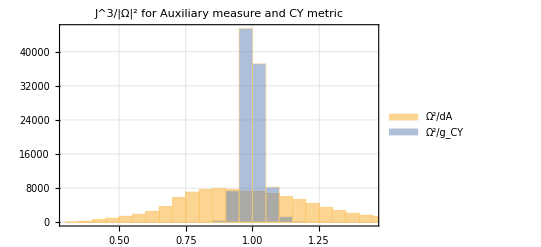

```mathematica
Histogram[{weights/Mean[weights],weightsCY/Mean[weightsCY]},PlotLabel->"J^3/|Ω|^2 for Auxiliary measure and CY metric",PlotTheme->"Detailed",ChartLegends->{ "Ω^2/dA","Ω^2/g_CY"}]
```

To actually access the CY metric, we just call CYMetric on some points

```mathematica
metrics=CYMetric[{{1,2,3,4,5}}];
(*NOTE: The code does not check whether the point is actually on the CY*)
```

```mathematica
metrics=CYMetric[pts];
```

```mathematica
metrics[[1]]//Chop//MatrixForm
```

(0.117129-1.28057×10^-9 ⅈ | 0.0028318+0.00793517 ⅈ | 0.0105414+0.0223561 ⅈ
0.0028318-0.00793517 ⅈ | 0.103159+9.8953×10^-10 ⅈ | -0.0136983-0.0139534 ⅈ
0.0105414-0.0223561 ⅈ | -0.0136983+0.0139534 ⅈ | 0.112784+2.32831×10^-10 ⅈ)

And the volume can be computed by integrating det(g). We compare the Kahler classes of the Fubini-Study and the CY metric, and also look at the actual value as computed from ∫J^3

```mathematica
auxWeights=GetAuxiliaryWeights["all"];
gFSs=FSMetric[pts,{1}];
gCYs=CYMetric[pts];
volFS=Round[Mean[Re[auxWeights (Det/@gFSs)]],0.1];
volCY=Round[Mean[Re[auxWeights (Det/@gCYs)]],0.1];
volInt=5;
Print["Kahler moduli:  ",{1}];
Print["Actual volume:  ",volInt];
Print["FS volume:      ",volFS];
Print["CY volume:      ",volCY];
```

Kahler moduli:  {1}

Actual volume:  5

FS volume:      5.

CY volume:      5.

For the Phi Model, we can also get the Kahler potential

```mathematica
kahler=GetKahlerPotential[pts];
kahler[[;;10]]
```

{0.328003,0.294206,0.341697,0.350628,0.2517,0.257643,0.293327,0.251553,0.285843,0.287078}

### Plot losses

```mathematica
history
```

<|sigma_loss→{0.161506,0.127558,0.100382,0.0844527,0.0786316,0.0753507,0.0719662,0.0701932,0.069417,0.0683528,0.0676854,0.0672523,0.0666325,0.0662399,0.0656526,0.0653093,0.0649564,0.0642834,0.0634489,0.0625384,0.0612094,0.0601294,0.0587451,0.0575448,0.0561747,0.0545453,0.0528727,0.0510253,0.0490354,0.0474367,0.0460083,0.0446611,0.0434437,0.0422694,0.0412269,0.0401281,0.039416,0.0385465,0.0377433,0.0372101,0.0364471,0.0358251,0.0350636,0.034366,0.0335409,0.0327322,0.0318112,0.0311377,0.0303789,0.0297212},kaehler_loss→{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},transition_loss→{0.00555381,0.00236893,0.00252454,0.0021886,0.00178435,0.00151204,0.00124271,0.00103625,0.000924976,0.000808117,0.000729431,0.000669969,0.000632045,0.00057992,0.000539704,0.000523443,0.000508176,0.000495878,0.000508004,0.000508919,0.00053051,0.000547115,0.000538084,0.000561713,0.000568579,0.000605532,0.000620716,0.000656036,0.000669734,0.000670843,0.000652542,0.000640534,0.0006185,0.00060136,0.000571825,0.00055361,0.00053817,0.000515424,0.000489965,0.000474854,0.000462195,0.000435924,0.000427323,0.000410194,0.000392626,0.000373084,0.000353113,0.000329879,0.000316104,0.000306365},ricci_loss→{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},sigma_val→{0.13317,0.111256,0.0976588,0.0872256,0.0820675,0.0800537,0.0762164,0.0771138,0.0760514,0.0751125,0.0747849,0.0743746,0.0740444,0.0754804,0.074633,0.0738001,0.0728842,0.0724806,0.0709871,0.0718881,0.0690101,0.0680953,0.0667803,0.0641863,0.0625917,0.0606075,0.0569503,0.0562965,0.0533878,0.0528378,0.0508666,0.0472707,0.0471389,0.0456457,0.0440276,0.0442379,0.0444127,0.0427669,0.041171,0.0401935,0.0384806,0.0390362,0.0381209,0.0366997,0.0362191,0.0346474,0.034176,0.0332592,0.032856,0.0316171},kaehler_val→{5.56285×10^-15,5.87313×10^-15,6.39338×10^-15,6.34354×10^-15,6.29746×10^-15,6.04402×10^-15,6.16258×10^-15,6.09701×10^-15,5.97775×10^-15,6.04263×10^-15,6.00461×10^-15,6.01438×10^-15,6.0711×10^-15,6.04418×10^-15,5.89882×10^-15,5.87945×10^-15,6.05954×10^-15,5.96545×10^-15,5.95886×10^-15,5.98356×10^-15,5.98613×10^-15,5.98745×10^-15,6.06606×10^-15,6.00846×10^-15,6.13574×10^-15,6.09739×10^-15,6.08859×10^-15,6.24304×10^-15,6.22341×10^-15,6.37906×10^-15,6.42602×10^-15,6.33784×10^-15,6.60269×10^-15,6.51439×10^-15,6.53164×10^-15,6.47985×10^-15,6.32818×10^-15,6.52556×10^-15,6.54511×10^-15,6.55517×10^-15,6.55048×10^-15,6.53385×10^-15,6.44489×10^-15,6.51882×10^-15,6.46422×10^-15,6.53671×10^-15,6.44101×10^-15,6.39969×10^-15,6.41247×10^-15,6.33059×10^-15},transition_val→{0.00312154,0.00216937,0.0025323,0.00183202,0.00153725,0.00151107,0.00107075,0.000945184,0.000828253,0.000743432,0.000640006,0.000625987,0.000594145,0.000509967,0.000475504,0.000499641,0.000523805,0.000516586,0.00053548,0.000644208,0.000522523,0.000569692,0.000560272,0.000536731,0.000554131,0.000604576,0.000632852,0.000675914,0.000652395,0.00064281,0.000634937,0.000618697,0.000608217,0.000596024,0.00054223,0.000517931,0.000527835,0.000476388,0.000468104,0.000464004,0.000440865,0.00042164,0.000436682,0.000429602,0.000379256,0.000412075,0.000370079,0.000353476,0.000323404,0.000297301},ricci_val→{1.11326,0.612845,0.635567,0.56971,0.581499,0.578902,0.549973,0.549657,0.516449,0.505955,0.5098,0.524115,0.498166,0.489744,0.485337,0.485869,0.508259,0.495798,0.479575,0.476229,0.472101,0.469756,0.463574,0.460965,0.450501,0.455439,0.445281,0.45088,0.444093,0.451888,0.432239,0.43846,0.451041,0.446845,0.434139,0.431565,0.418975,0.418248,0.411258,0.428185,0.414037,0.40383,0.399939,0.401321,0.400435,0.38309,0.378111,0.384314,0.380201,0.381559},volk_val→{5.25534,5.10056,4.91081,5.01047,5.06453,4.75847,5.08494,4.86422,4.99503,4.98604,4.91188,4.94562,4.86999,4.94758,4.90632,4.83609,4.95417,4.8137,4.87383,4.858,4.92131,4.96365,4.93772,4.93533,4.97566,4.96762,4.98091,4.96851,4.90395,4.96186,4.94278,4.97623,4.94363,4.98072,4.93838,4.96218,4.91351,4.98634,4.98174,4.98542,4.98065,4.97262,4.94828,4.98659,5.00549,4.97665,5.01,4.99856,4.97924,5.01413}|>

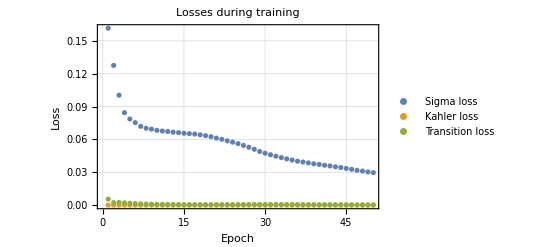

```mathematica
ListPlot[{history[["sigma_loss"]],history[["kaehler_loss"]],history[["transition_loss"]]},PlotLabel->"Losses during training",FrameLabel->{"Epoch","Loss"},PlotLegends->{"Sigma loss", "Kahler loss","Transition loss"},PlotTheme->"Detailed"]
```

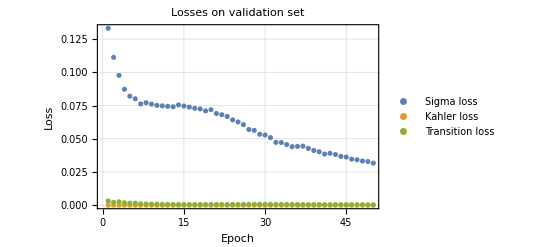

```mathematica
ListPlot[{history[["sigma_val"]],history[["kaehler_val"]],history[["transition_val"]]},PlotLabel->"Losses on validation set",FrameLabel->{"Epoch","Loss"},PlotLegends->{"Sigma loss", "Kahler loss","Transition loss"},PlotTheme->"Detailed"]
```

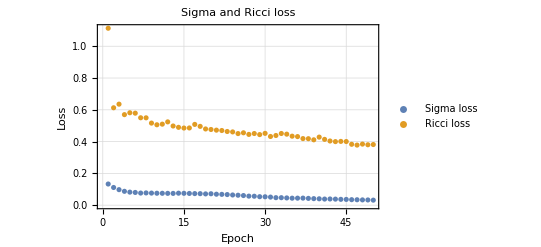

```mathematica
ListPlot[{history[["sigma_val"]],history[["ricci_val"]]},PlotLabel->"Sigma and Ricci loss",FrameLabel->{"Epoch","Loss"},PlotLegends->{"Sigma loss", "Ricci loss"},PlotTheme->"Detailed"]
```

```mathematica
SigmaVsRicci=Table[{history[["sigma_val"]][[i]],history[["ricci_val"]][[i]]},{i,Length[history[["sigma_val"]]]}];
```

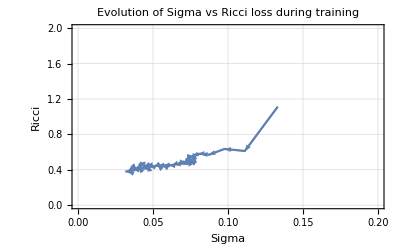

```mathematica
Show@@Join[{ListLinePlot[SigmaVsRicci,PlotLabel->"Evolution of Sigma vs Ricci loss during training",FrameLabel->{"Sigma","Ricci"},PlotRange->{{0,0.2},{0,2}},PlotTheme->"Detailed"]},Table[ListLinePlot[SigmaVsRicci[[i;;i+1]],PlotStyle->Directive[Thick,Arrowheads[.035]]]/.Line->Arrow,{i,Length[SigmaVsRicci]-1}]]
```

### Look at eigenvalues of the metric

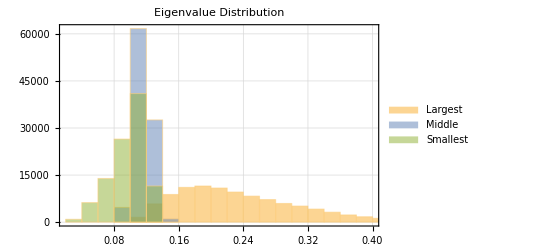

```mathematica
EigVals=Table[Eigenvalues[metrics[[i]]]//Re//Chop,{i,Length[metrics]}];
Histogram[{EigVals[[;;,1]],EigVals[[;;,2]],EigVals[[;;,3]]},PlotLabel->"Eigenvalue Distribution",PlotTheme->"Detailed",ChartLegends->{"Largest", "Middle","Smallest"}]
```